# SU(2)紧聚焦仿真

Lawrence Lee

北京理工大学

2020.11.9

旨在说明如何处理

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

自动计算的部分

```mathematica
<<MaTeX`
<<Notation`
<<MATLink`
OpenMATLAB[]
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[γ, 0]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[x, ∞]]
Symbolize[Subscript[y, ∞]]
Symbolize[Subscript[z, ∞]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[OverVector[Subscript[Ε, ∞]]]
Symbolize[OverVector[Subscript[Ε, int]]]
Symbolize[OverVector[Subscript[n, ϕ]]]
Symbolize[OverVector[Subscript[n, ρ]]]
Symbolize[OverVector[Subscript[n, θ]]]
Symbolize[Subscript[ℓ, 1]]
Symbolize[Subscript[ℓ, 2]]
Symbolize[(e⃗)_R]
Symbolize[(e⃗)_L]
Symbolize[(e⃗)_x]
Symbolize[(e⃗)_y]
Symbolize[Subscript[β, 0]]
Symbolize[Subscript[ρ, s]]
Symbolize[Subscript[ρ, max]]
```

```mathematica
<<Notation`
Symbolize[Subscript[I, 00]]
Symbolize[Subscript[I, 01]]
Symbolize[Subscript[I, 02]]
Symbolize[Subscript[I, 10]]
Symbolize[Subscript[I, 11]]
Symbolize[Subscript[I, 12]]
Symbolize[Subscript[I, 13]]
Symbolize[Subscript[I, 14]]
Symbolize[Subscript[f, ω]]
Symbolize[Subscript[θ, max]]
Symbolize[Subscript[f, 0]]
Symbolize[Subscript[ω, 0]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[Ε, x]]
Symbolize[Subscript[Ε, y]]
Symbolize[Subscript[Ε, z]]
Symbolize[𝕀]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

## 3. HLG为基模

### 1. 修改说明

加入了变量

为避免与紧聚焦公式中的混淆，将此处的改为

将初相位改为

令，，

### 2. 代码

#### 1. 输入参数

固定参数

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*输入波长，单位um*)
λ=0.532;
```

可调参数

```mathematica
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*输入固有横模指数n*)
n=10.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=20.;
(*输入固有纵模指数l*)
l=1.;
(*输入庞加莱球上的坐标(α,β)*)
α=π/2;
β=π/2;
(*输入初相位*)
γ=π/2;
(*输入相干叠加次数M*)
M=4.;
(*输入坐标范围a*)
r=3;
(*绘制2D图*)
z=0;
```

计算腔径，需首先清楚R的赋值

```mathematica
(*-Graphics-,令-Graphics-计算-Graphics-*)
R=.
L=1.;
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
```

#### 2. 定义函数

```mathematica
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,l_] ⟺ l_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,l_] ⟺ 2π Subscript[f, n_,m_,l_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

#### 3. 绘图

```mathematica
DensityPlot[#,{x,-r,r},{y,-r,r},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,PlotPoints->150,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-}}//Column//CloudDeploy

SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/33db8d1e-60a4-41ca-a848-c8696b6d2eae]

## 4. LG作为本征基

直接以LG为本征矢，故对应庞加莱球上的南北极两点，此时将不再需要α，β参量

#### 1. 输入参数

固定参数

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*输入波长，单位um*)
λ=0.532;
```

可调参数

```mathematica
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
(*输入初相位*)
γ=π/2;
(*输入相干叠加次数M*)
M=4.;
(*输入坐标范围a*)
a=3;
(*绘制2D图*)
z=0;
```

计算腔径，需首先清楚R的赋值

```mathematica
(*-Graphics-,令-Graphics-计算-Graphics-*)
R=.
L=1.;
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
```

#### 2. 定义函数

```mathematica
(*拉盖尔多项式*)
Notation[Subscript[L, 𝓅_]^ℓ_[x_] ⟺ LaguerreL[𝓅_,Abs[ℓ_],x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[𝒞, 𝓅_,ℓ_] ⟺ √(2/π(𝓅_!)/((𝓅_+Abs[ℓ_])!))]

Notation[Subscript[r̃, (x_,y_,z_)] ⟺ (√(2(x_^2+y_^2)))/w[z_]]
Notation[Subscript[𝓅, (n_,m_)] ⟺ Min[n_,m_]]
Notation[Subscript[ℓ, (n_,m_)] ⟺ m_-n_]
Notation[Subscript[θ, (x_,y_)] ⟺ ArcTan[x_,y_]]

Notation[Subscript[Ψ, n_,m_,l_]^(LG)[x_,y_,z_] ⟺ Subscript[𝒞, Subscript[𝓅, (n_,m_)],Subscript[ℓ, (n_,m_)]]/w[z_](Subscript[r̃, (x_,y_,z_)])^Abs[Subscript[ℓ, (n_,m_)]] Exp[-(Subscript[r̃, (x_,y_,z_)]/(√2))^2]Subscript[L, Subscript[𝓅, (n_,m_)]]^Subscript[ℓ, (n_,m_)][Subscript[r̃, (x_,y_,z_)]^2]Exp[ⅈ Subscript[ℓ, (n_,m_)] Subscript[θ, (x_,y_)]]Exp[ⅈ Subscript[k, n_,m_,l_] z̃[x_,y_,z_]-ⅈ(2 Subscript[𝓅, (n_,m_)]+Abs[Subscript[ℓ, (n_,m_)]]+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(LG)[x_,y_,z_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_])*//Norm]
```

#### 3. 绘图

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,PlotPoints->150,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,γ,M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,γ,M],,-Graphics-,-Graphics-}}//Column//CloudDeploy

SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/75f73e87-f163-49b0-8044-c2a7b656e09b]

## 7. 绘图技巧 & 问题

#### 1. 同时绘制两张带不同标签的图

用Table和Apply

```mathematica
Table[Plot[#,{x,-10,10},PlotLabel->#2,ImageSize->Large]&@@n,{n,{{Sin[x],"图1"},{Cos[x],"图2"}}}]//Column
```

用Apply to level 1

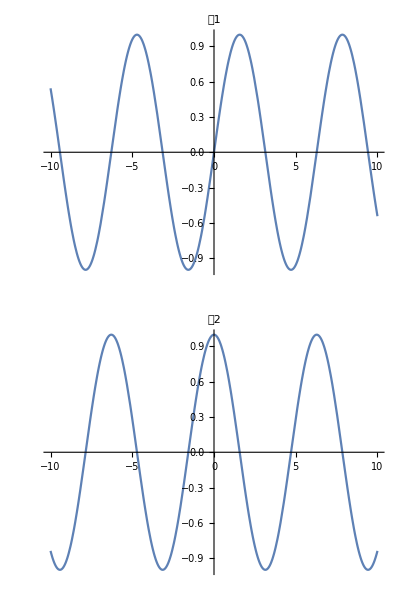

```mathematica
Plot[#,{x,-10,10},PlotLabel->#2,ImageSize->Large]&@@@{{Sin[x],"图1"},{Cos[x],"图2"}}//Column
```

#### 2. 去掉标签中数字后跟的、表示浮点精度的

若为整数或分数

```mathematica
SetPrecision[1/4,∞]
```

1/4

若为小数

```mathematica
SetPrecision[0.1,∞]
```

3602879701896397/36028797018963968

上述方式失效，改为以下代码

```mathematica
With[{r=Round[#]},r+Chop[#-r]]&@@0.1
```

0.1

#### 3. 添加PlotLegends的代码

此时，ImageSize→{750,750}

此外，最好还应给出LG光中拓扑荷与径向指数的值，关系为

```mathematica
{{-Graphics-, , }, {-Graphics-, -Graphics-, SetPrecision[M,∞]}, {-Graphics-, -Graphics-, SetPrecision[Ω,∞]}, {-Graphics-, -Graphics-, SetPrecision[p,∞]}, {-Graphics-, -Graphics-, SetPrecision[Q-p,∞]}, {-Graphics-, -Graphics-, SetPrecision[P,∞]}, {-Graphics-, -Graphics-, γ}, {-Graphics-, , }, {-Graphics-, -Graphics-, α}, {-Graphics-, -Graphics-, β}, {-Graphics-, , }, {-Graphics-, -Graphics-, SetPrecision[n,∞]}, {-Graphics-, -Graphics-, SetPrecision[m,∞]}, {-Graphics-, -Graphics-, SetPrecision[l,∞]}, {-Graphics-, , }, {-Graphics-, -Graphics-, SetPrecision[Min[n,m],∞]}, {-Graphics-, -Graphics-, SetPrecision[n-m,∞]}}//Grid[#,Frame->Bottom,Background->LightBlue]&
```

-Graphics- |  | 
-Graphics- | -Graphics- | 4
-Graphics- | -Graphics- | 1/4
-Graphics- | -Graphics- | -1
-Graphics- | -Graphics- | 5
-Graphics- | -Graphics- | 1
-Graphics- | -Graphics- | ϕ_0
-Graphics- |  | 
-Graphics- | -Graphics- | π/2
-Graphics- | -Graphics- | π/2
-Graphics- |  | 
-Graphics- | -Graphics- | 15
-Graphics- | -Graphics- | 30
-Graphics- | -Graphics- | 1
-Graphics- |  | 
-Graphics- | -Graphics- | 15
-Graphics- | -Graphics- | -15

```mathematica
{{-Graphics-, , }, {-Graphics-, -Graphics-, 4}, {-Graphics-, -Graphics-, 1/4}, {-Graphics-, -Graphics-, -1}, {-Graphics-, -Graphics-, 5}, {-Graphics-, -Graphics-, 1}, {-Graphics-, -Graphics-, π/2}, {-Graphics-, , }, {-Graphics-, -Graphics-, π/2}, {-Graphics-, -Graphics-, π/2}, {-Graphics-, , }, {-Graphics-, -Graphics-, 15}, {-Graphics-, -Graphics-, 30}, {-Graphics-, -Graphics-, 1}, {-Graphics-, , }, {-Graphics-, -Graphics-, 15}, {-Graphics-, -Graphics-, -15}}
```

#### 4. 用FrameLabel添加“态”

```mathematica
FrameLabel->-Graphics-
```

#### 5. 用PlotLabel说明绘制的是相位图还是光强图

```mathematica
PlotLabel->-Graphics-
```

#### 6. 相应的MaTeX代码

```mathematica
MaTeX["\\Psi_{n+p K, m+(Q-p) K, l-P K}^{\\mathrm{SU}(2)}\\left(x, y, z, \\alpha, \\beta, \\gamma, M\\right)",Magnification->2]
```

-Graphics-

HLG模使用

```mathematica
MaTeX["\\left|\\Psi_{n, m, l}^{M, P,p,q}\\right\\rangle",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\left|\\Psi_{n+p K, m+(Q-p)K, l-P K}^{M, \\Omega, \\alpha,\\beta,\\gamma}\\right\\rangle",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\mathcal{P}_{n+p K, m+(Q-p)K, l-P K}^{M, \\Omega, \\alpha,\\beta,\\gamma}(x,y,0)",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\mathcal{I}_{n+p K, m+(Q-p)K, l-P K}^{M, \\Omega, \\alpha,\\beta,\\gamma}(x,y,0)",Magnification->2]
```

-Graphics-

LG模使用

```mathematica
MaTeX["\\left|\\Psi_{n+p K, m+(Q-p)K, l-P K}^{M, \\Omega, \\frac{\\pi}{2},\\frac{\\pi}{2},\\gamma}\\right\\rangle",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\mathcal{P}_{n+p K, m+(Q-p)K, l-P K}^{M, \\Omega, \\frac{\\pi}{2},\\frac{\\pi}{2},\\gamma}(x,y,0)",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\mathcal{I}_{n+p K, m+(Q-p)K, l-P K}^{M, \\Omega, \\frac{\\pi}{2},\\frac{\\pi}{2},\\gamma}(x,y,0)",Magnification->2]
```

-Graphics-

#### 7. 使用Binomial函数

M!/(K!(M-K)!)⟶√Binomial[M,K]

#### 8. 效果

```mathematica
Plot[#,{x,-10,10},Background->White,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{Sin[x],,-Graphics-,-Graphics-},{Cos[x],,-Graphics-,-Graphics-}}//Column//CloudDeploy

SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/d9744f4f-444f-44e4-b496-6bfb895e45b9]

#### 9. 转换为柱坐标系后的作图问题

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*-Graphics-,令-Graphics-计算-Graphics-*)
L=1.;
(*输入波长，单位um*)
λ=0.532;
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*计算腔径,需首先清楚R的赋值*)
R=.
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
M=4.;
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

```mathematica
n=2
m=1
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->50,ImageSize->Medium]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π,π 3/2,π,0],(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π,π 3/2,π,0]}//Rasterize[#,RasterSize->500]&
```

2

1

-Graphics-

方案，先用极坐标进行推导，最后在转换到直角坐标中用DensityPlot绘图

举例

```mathematica
f[x_,y_]:=x^2+y^2
DensityPlot[f[x,y],{x,-10,10},{y,-10,10}]//Rasterize[#,RasterSize->400]&
DensityPlot[f[r Cos[θ],r Sin[θ]]/.{r->√(x^2+y^2),θ->ArcTan[x,y]},{x,-10,10},{y,-10,10}]//Rasterize[#,RasterSize->400]&
```

-Graphics-

-Graphics-

实战

```mathematica
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->50,ImageSize->Medium]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[r Cos[θ],r Sin[θ],0,π/2,π/2,π/2,M]/.{r->√(x^2+y^2),θ->ArcTan[x,y]},(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[r Cos[θ],r Sin[θ],0,π/2,π/2,π/2,M]/.{r->√(x^2+y^2),θ->ArcTan[x,y]}}//Rasterize[#,RasterSize->500]&//AbsoluteTiming
```

{20.2787,-Graphics-}

## SU(2)光紧聚焦

## 2. 模

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ*Subscript[I, 11][ρ]Cos[φ]+ⅈ*Subscript[I, 14][ρ]Cos[3φ]}, {-ⅈ*Subscript[I, 12][ρ]Sin[φ]+ⅈ*Subscript[I, 14][ρ]Sin[3φ]}, {-2*Subscript[I, 10][ρ]+2*Subscript[I, 13][ρ]*Cos[2φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 3. 模

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]+2*Subscript[I, 12][ρ])Sin[φ]+ⅈ*Subscript[I, 14][ρ]Sin[3φ]}, {-ⅈ*Subscript[I, 12][ρ]Cos[φ]-ⅈ*Subscript[I, 14][ρ]Cos[3φ]}, {2*Subscript[I, 13][ρ]Sin[2φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.000000001,3,.01},{φ,0,2π,.001}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 4. 径向偏振

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]-Subscript[I, 12][ρ])Cos[φ]}, {ⅈ(Subscript[I, 11][ρ]-Subscript[I, 12][ρ])Sin[φ]}, {-4*Subscript[I, 10][ρ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度和相位

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,8,.05},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 5. 角向偏振

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]+3 Subscript[I, 12][ρ])Sin[φ]}, {-ⅈ(Subscript[I, 11][ρ]+3 Subscript[I, 12][ρ])Cos[φ]}, {0}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.000000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度和相位

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,0.3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 3. HLG为基模

### 1. 修改说明

加入了变量

为避免与紧聚焦公式中的混淆，将此处的改为

将初相位改为（变量）和（常量）

### 2. 代码

#### 1. 输入参数

固定参数

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*输入波长，单位um*)
λ=0.532;
```

可调参数

```mathematica
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
(*输入庞加莱球上的坐标(α,β)*)
α=π/2;
β=π/2;
(*输入初相位*)
γ=π/2;
(*输入相干叠加次数M*)
M=4.;
(*输入坐标范围a*)
a=3;
(*绘制2D图*)
z=0;
```

计算腔径，需首先清楚R的赋值

```mathematica
(*-Graphics-,令-Graphics-计算-Graphics-*)
R=.
L=1.;
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
```

#### 2. 定义函数

```mathematica
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

#### 3. 绘图

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,PlotPoints->150,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-}}//Column//CloudDeploy

SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/737cac44-4430-4b9a-b576-93a91db93e87]

## 1. SU(2)模

```mathematica
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
NA=1.3;
Subscript[θ, max]=.
Subscript[θ, max]=Solve[NA==Subscript[n, 2]*Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]⟦1,1⟧/.Rule->Set;

f=0.481;(*100倍物镜的焦距一般为0.13~0.19mm*)
k=(2π)/λ;
Notation[Subscript[f, 0] ⟺ Subscript[w, 0]/(f Sin[Subscript[θ, max]])]
 Subscript[Ε, 0]=100;
Subscript[f, 0]
```

0.998997

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_,ϕ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max],0]
```

-0.0420336+0.0402489 ⅈ

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[0],f Sin[θ_]Sin[0],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max]]
```

-0.0420336+0.0402489 ⅈ

#### 1. 初始设置

```mathematica
(*定义Subscript[I, ij]*)
Subscript[I, 00][ρ_]:=NIntegrate[(((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) Sin[θ]) (1+Cos[θ])) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 01][ρ_]:=NIntegrate[((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) (-Sin[θ])^2) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 02][ρ_]:=NIntegrate[(((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) Sin[θ]) (1-Cos[θ])) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
```

```mathematica
Subscript[I, 00][1]
Subscript[I, 01][1]
Subscript[I, 02][1]
```

0.000993794-0.000973806 ⅈ

0.000874985-0.00084987 ⅈ

-0.0000432257+0.0000433869 ⅈ

#### 2. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f)/2)√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{Subscript[I, 00][ρ]+Subscript[I, 02][ρ]Cos[2φ]}, {Subscript[I, 02][ρ]Sin[2φ]}, {-2*ⅈ*Subscript[I, 01][ρ]Cos[φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

```mathematica
Ε[1,1]
```

{{-0.106005-0.137698 ⅈ},{0.00423008+0.00536262 ⅈ},{-0.128554+0.0980236 ⅈ}}

#### 3. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,.0001,3,1},{φ,0,2π,1}];//AbsoluteTiming
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,.00000001,3,1},{φ,0,2π,1}];//AbsoluteTiming
```

$Aborted

LinkObject::linkd: Unable to communicate with closed link LinkObject["A:\Program Files\Wolfram Research\Mathematica\12.1\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,2685,11].

KernelObject::rdead: Subkernel connected through … appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {46} assigned to ….

LaunchKernels::clone: Kernel … resurrected as ….

```mathematica
data//Dimensions
Flatten[data,1]//Dimensions
```

{300,629,3}

{188700,3}

```mathematica
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
```

```mathematica
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 4. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 2

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[0],f Sin[θ_]Sin[0],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max]]
```

-0.0420336+0.0402489 ⅈ

```mathematica
HankelTransform
```

按照Focusing of high numerical aperture cylindricalvector beams的方法算径向偏振

```mathematica
<<Notation`
```

```mathematica
(*Notation[Ψ^(SU(2))[ρ_] ⟺ NIntegrate[√Cos[θ] Sin[2θ]Ψ_(-Graphics-)^(SU(2))[θ]BesselJ[1,(k ρ_) Sin[θ]],{θ,0,Subscript[θ, max]}]]
Notation[𝒫^(SU(2))[ρ_] ⟺ Arg[Ψ^(SU(2))[ρ_]]//Norm]
Notation[𝕀^(SU(2))[ρ_] ⟺ Ψ^(SU(2))[ρ_]*(Ψ^(SU(2))[ρ_])*//Norm]*)
```

```mathematica
Ψ[ρ_]:=NIntegrate[√Cos[θ] Sin[2θ](Ψ_(-Graphics-)^(SU(2)))[θ]BesselJ[1,(k ρ) Sin[θ]],{θ,0,Subscript[θ, max]}]
𝒫[ρ_]:=Arg[Ψ[ρ]]//Norm
𝕀[ρ_]:=Ψ[ρ]*(Ψ[ρ])*//Norm
```

```mathematica
Ψ[1]
𝒫[1]
𝕀[1]
```

-0.000643742+0.000630456 ⅈ

2.36662

8.11878×10^-7

```mathematica
a
```

3

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,ImageSize->{750,750},Frame->True]&@@@{{𝒫[√(x^2+y^2)]},{𝕀[√(x^2+y^2)]}}//Column//CloudDeploy

SystemOpen[%]
```

NIntegrate::inumr: The integrand 0.25 BesselJ[1,11.8105 √(x^2+y^2) Sin[θ]] √Cos[θ] («1») Sin[2 θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.02824}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

SystemOpen[$Aborted]

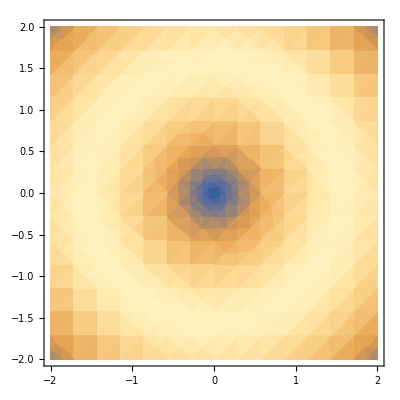

```mathematica
DensityPlot[Sin[√(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

```mathematica
DensityPlot[Sin[√(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

# 汉克儿变换推导线偏光的衍射积分

公式

-Graphics-

并不现实，因为积分式太难求

```mathematica
<<MaTeX`
<<Notation`
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[γ, 0]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[x, ∞]]
Symbolize[Subscript[y, ∞]]
Symbolize[Subscript[z, ∞]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[OverVector[Subscript[Ε, ∞]]]
Symbolize[OverVector[Subscript[Ε, int]]]
Symbolize[OverVector[Subscript[n, ϕ]]]
Symbolize[OverVector[Subscript[n, ρ]]]
Symbolize[OverVector[Subscript[n, θ]]]
Symbolize[Subscript[ℓ, 1]]
Symbolize[Subscript[ℓ, 2]]
Symbolize[(e⃗)_R]
Symbolize[(e⃗)_L]
Symbolize[(e⃗)_x]
Symbolize[(e⃗)_y]
Symbolize[Subscript[β, 0]]
Symbolize[Subscript[ρ, s]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
f=1;
w[0];
```

```mathematica
Notation[Subscript[Ψ, n_,m_]^(SU(2))[θ_,ϕ_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)(∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ K γ_] (Exp[1/2 ⅈ (n_+m_) α_] ∑_(k=0)^(n_+m_) (Exp[ⅈ k α_] Subscript[d, n_,m_]^k[β] (√(2/L) (Subscript[H, k][ Cos[ϕ_] ] Subscript[H, n_+m_-k][Sin[ϕ_]] Exp[-(f Sin[θ_])^2/w[0]^2]) Exp[-ⅈ ((n_+m_-k)+k+1) ϑ[0]]))/(√(2^((n_+m_-k)+k-1) π (n_+m_-k)! k!) w[0])))]
```

Notation::expatnf: Pattern 'β' appearing in the external representation 'Notation`Private`identityForm[RowBox[{SubsuperscriptBox[Ψ,RowBox[{n_,,,m_}],RowBox[{SU,RowBox[{«3»}]}]],[,RowBox[{θ_,,,ϕ_,,,α_,,,β_,,,γ_,,,M_}],]}]]' cannot be filled since 'β' does not appear in the internal representation 'Notation`Private`identityForm[TagBox[RowBox[{FractionBox[1,SuperscriptBox[2,RowBox[{«3»}]]],RowBox[{(,RowBox[{«2»}],)}]}],HoldForm]]'.

$Failed

```mathematica
1/2^(M/2)(∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ] (Exp[1/2 ⅈ (n+m) α] ∑_(k=0)^(n+m) (Exp[ⅈ k α] (Subscript[d, n,m]^k)[β] (√(2/L) (Subscript[H, k][ Cos[ϕ] ] Subscript[H, n+m-k][Sin[ϕ]] Exp[-(f Sin[θ])^2/w[0]^2]) Exp[-ⅈ ((n+m-k)+k+1) ϑ[0]]))/(√(2^((n+m-k)+k-1) π (n+m-k)! k!) w[0])))
```

# ML代码

基于尼康100倍油浸物选取参数，参数为：

入射光半径

```mathematica
λ=0.532;
Subscript[ρ, max]=1000λ;
```

透镜最大汇聚角

对于大NA物镜，不能认为

```mathematica
NA=1.3;
Subscript[n, 2]=1.518;
```

Solve[NA==n_2 Sin[θ_max],θ_max,InverseFunctions→True]/.Rule→Set;

结果为

```mathematica
Subscript[θ, max]=1.0282369130485443;
```

NA=1.3;
n_2=1.518;
theta_max=asin(NA/n_2)

theta_max =

    1.0282

透镜焦距

tan(θ_max)=ρ_max/f
f=ρ_max/(tan(θ_max))

化简

ρ_max/Tan[ArcSin[NA/n_2]]

结果为

误差分析

```mathematica
Subscript[n, 2]=1.518;
NA=1.3;
(*实际表达式*)
f=(√(1-(NA/Subscript[n, 2])^2)Subscript[n, 2] Subscript[ρ, max])/NA
(*杰哥的表达式*)
f=Subscript[ρ, max]/NA
```

320.75

409.231

令n_1=1计算误差

```mathematica
NA=0.95;
(*实际表达式*)
f=Subscript[ρ, max]/Tan[ArcSin[NA]]
(*杰哥的表达式*)
f=Subscript[ρ, max]/NA
```

174.86

560.

可见，杰哥所用的方式，带来的误差必然很大

%波长%
lambda=0.532;
%入瞳半径%
rho_max=1000*lambda;
%透镜焦距%
f=sqrt(1-(NA/n_2)^2)*n_2*rho_max/NA

f =

  320.7503

入射光的方位角

N_theta=151;
N_varphi=153;
theta=linspace(0,theta_max,N_theta);
varphi=linspace(0,2*pi,N_varphi);
[Theta,Varphi]=meshgrid(theta,varphi);
Rho=f*sin(Theta);
X=Rho.*cos(Varphi);
Y=Rho.*sin(Varphi);

为何此处不采用...

#### HG_21

HG_21

%束腰%
w=rho_max/3;
m=2;
n=1;

HermitePoly是厄米多项式的零点

%束腰%
w=rho_max/3;
m=2;
n=1;
Hx=polyval(HerrmitePoly(m),sqrt(2)*X/w);
Hy=polyval(HermitePoly(n),sqrt(2)*Y/w);
rc=sqrt(2^(1-n-m)/(pi*factorial(n)*factorial(m)))/w;

基变换得径向和角向分量

出瞳面上的光场分布

E_ρ=√(cos(θ))cos(θ)LP
E_φ=√(cos(θ))AP
E_z=√(cos(θ))sin(θ)LP

聚焦积分

N_xo=51;
N_yo=53;
r_max=2*lambda;
xo=linspace(-r_max,r_max,N_xo);
yo=linspace(-r_max,r_max,N_yo);
[Xo,Yo]=meshgrid(xo,yo);
R=sqrt(Xo.^2+Yo.^2);
Phi=angle(Xo+1i*Yo);

衍射积分

[m,n]=size(R);

for nn=1:n
	for mm=1:m

MATLink::errx: Error: File: C:\Users\Lee\AppData\Local\Temp\MATLink20121014292567AuqDnSdVcE\input.m Line: 5 Column: 1
     At least one END is missing: the statement may begin here.

$Failed

为何√cos(θ)是透镜

C

"☆"

## 附

输入常数C[1]

```mathematica
C[1]//FullForm
```

C[1]

polyval函数

y = polyval([3, 2, 1],[5])

y =

    86

```mathematica
x=5
3x^2+2x+1
```

5

86

求厄米多项式的零点

计算厄米多项式的个正整数值，所得矢量的元为的系数计算

function [ H ] = HermitePoly( n )
if n==0
    H=1;
elseif n==1
    H=[2 0];
else
    hpm2=zeros(1,n+1);
    hpm2(n+1)=1;
    hpm1=zeros(1,n+1);
    hpm1(n)=2;
    for k=2:n
        H=zeros(1,n+1);
        for r=n-k+1:2:n
            H(r)=2*(hpm1(r+1)-(k-1)*hpm2(r));
        end
        H(n+1)=-2*(k-1)*hpm2(n+1);
        if k<n
            hpm2=hpm1;
            hpm1=H;
        end
    end
end
end

y =

    86

所实现的功能完全同

```mathematica
HermiteH[2,√2 x/w]
```

6

.